```mathematica
f1 = Piecewise[{{3 Abs@x,Abs@x≤  π/2},{0,Abs@x>π/2}}]
```

Piecewise[{{3 Abs[x], Abs[x]≤π/2}, {0, True}}]

```mathematica
f2 = Piecewise[{{3 Abs[x-2π],Abs[x-2π]≤  π/2},{0,Abs[x-2π]>π/2}}]
```

Piecewise[{{3 Abs[-2 π+x], Abs[-2 π+x]≤π/2}, {0, True}}]

```mathematica
f3 = Piecewise[{{3 Abs[x+2π],Abs[x+2π]≤  π/2},{0,Abs[x+2π]>π/2}}]
```

Piecewise[{{3 Abs[2 π+x], Abs[2 π+x]≤π/2}, {0, True}}]

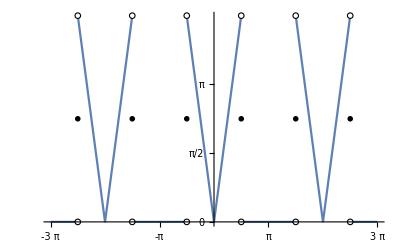

```mathematica
Plot[f1 + f2+f3, {x,-3π,3π}, Epilog-> {Disk[{π/2,3π/4},Offset[2]], Disk[{-π/2,3π/4},Offset[2]],Disk[{3π/2,3π/4},Offset[2]],Disk[{-3π/2,3π/4},Offset[2]],Disk[{5π/2,3π/4},Offset[2]],Disk[{-5π/2,3π/4},Offset[2]],{EdgeForm[Black],White,Disk[{π/2,0},Offset[2]]}, {EdgeForm[Black],White,Disk[{-π/2,0},Offset[2]]},{EdgeForm[Black],White,Disk[{3π/2,0},Offset[2]]}, {EdgeForm[Black],White,Disk[{-3π/2,0},Offset[2]]},{EdgeForm[Black],White,Disk[{5π/2,0},Offset[2]]}, {EdgeForm[Black],White,Disk[{-5π/2,0},Offset[2]]},{EdgeForm[Black],White,Disk[{π/2,3π/2},Offset[2]]}, {EdgeForm[Black],White,Disk[{-π/2,3π/2},Offset[2]]},{EdgeForm[Black],White,Disk[{3π/2,3π/2},Offset[2]]}, {EdgeForm[Black],White,Disk[{-3π/2,3π/2},Offset[2]]},{EdgeForm[Black],White,Disk[{5π/2,3π/2},Offset[2]]}, {EdgeForm[Black],White,Disk[{-5π/2,3π/2},Offset[2]]}}, Ticks->{Range[-3π,3π,π],Range[0,π,π /2]}]
```